-2/r+(2 ⅇ^(-r/2))/r

4/r^2+(4 ⅇ^-r)/r^2-(8 ⅇ^(-r/2))/r^2

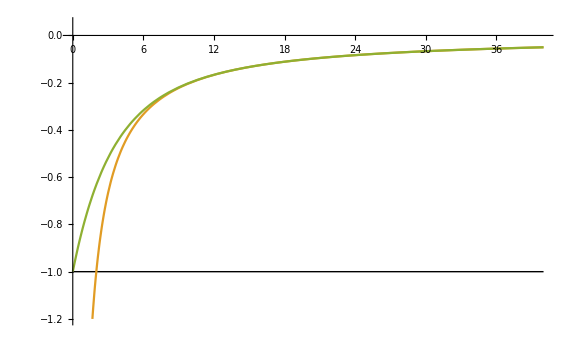
-Graphics-r/r_AUE/E_AU𝒩 = 1

```mathematica
Clear[g];
Block[{g,𝒩,U0,prec},
prec=240;
g[U0_,𝒩_,α_]:=-2/r(1-Exp[-α U0 r]/(2α)Sum[(α U0 r)^n/(n!)(2α-n),{n,0,𝒩}]);

U0=1;𝒩=1;
plt[xp_]:=Plot[
{Style[-U0,DotDashed],-2/r,xp},{r,0,20 2/(𝒩 U0)},
PlotRange->{-1.2*U0,0.05},
WorkingPrecision->prec,PerformanceGoal->"Quality",ImageSize->Large
];
Off[General::munfl];
(gexp=Collect[(g[U0,𝒩,𝒩/2]+2/r)/Exp[-𝒩/2 U0 r],r]Exp[-𝒩/2 U0 r]-2/r)//Print;
gexp^2//Expand//Print;
Labeled[plt[gexp],{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
];
```

-2/r+ⅇ^(-(9 r^2)/2) (-3+2/r+9 r-(27 r^2)/2+(81 r^3)/4)

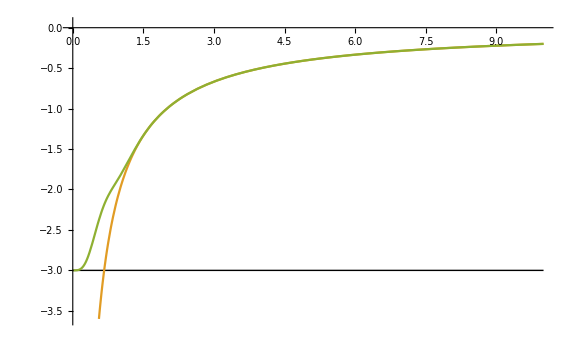
-Graphics-r/r_AUE/E_AU𝒩 = 2

```mathematica
Clear[g];
Block[{g,𝒩,U0,prec},
prec=240;
f[U0_,𝒩_,ℬ_]:=(1-(U0 r)/2)(Sum[(ℬ U0 r)^(2n)/(n!),{n,0,𝒩-1}])+(ℬ U0 r)^(2𝒩)/(𝒩!);
g[U0_,𝒩_,ℬ_]:=-2/r(1-Exp[-(ℬ U0 r)^2]f[U0,𝒩,ℬ]);
U0=3;𝒩=2;
plt[xp_]:=Plot[
{Style[-U0,DotDashed],-2/r,xp},{r,0,10},
PlotRange->{-1.2*U0,0.05},
WorkingPrecision->prec,PerformanceGoal->"Quality",ImageSize->Large
];
Off[General::munfl];
(gexp=Collect[(g[U0,𝒩,(√𝒩)/2]+2/r)/Exp[-((√𝒩)/2 U0 r)^2],r]Exp[-((√𝒩)/2 U0 r)^2]-2/r)//Print;
Labeled[plt[gexp],{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
];
```